```mathematica
$PrePrint = MatrixForm;
(* Pauli matrices *)
X = ({{0, 1}, {1, 0}}); Y = ({{0, -I}, {I, 0}}); Z = ({{1, 0}, {0, -1}}); ID = ({{1, 0}, {0, 1}});
```

## Lindbladian and Kraus Operators

```mathematica
(* example density matrix *)
ρ = ({{ρuu, ρud}, {ρdu, ρdd}});
```

### Depolarizing Channel

```mathematica
(* Lindbladian with single Subscript[σ, z] jump operator *)
lindbladZ = With[{J = ({{1, 0}, {0, -1}})(* jump operator*)},
	-Γ/2(KroneckerProduct[ID, J†.J] + KroneckerProduct[(J†.J)ᵀ, ID] - 2 KroneckerProduct[J*, J])
];
ρD = Partition[MatrixExp[lindbladZ].Flatten[ρ], 2];
Print["e^Lρ = ", ρD //MatrixForm];
```

e^Lρ = (ρuu | ⅇ^(-2 Γ) ρud
ⅇ^(-2 Γ) ρdu | ρdd)

```mathematica
(* Kraus operators for the Lindbladian above *)
{K1, K2} = {Cos[θ] ({{1, 0}, {0, 1}}), Sin[θ] Z} /. θ -> 1/2 ArcCos[ⅇ^(-2Γ)];
{K1, K2} = {Cos[θ]({{1, 0}, {0, 1}}), Sin[θ] Z} /. θ -> 1/2 ArcCos[1-Γ];
(*{K1, K2,K3,K4} = {Sqrt[1-3 Γ/4] ({{1, 0}, {0, 1}}), Sqrt[Γ/4] X,Sqrt[Γ/4] Y,Sqrt[Γ/4] Z}*)
Kraus = {K1, K2}; (*,K3,K4};*)
KrausConj = Kraus; (* complex conjugate *)
ρKraus = K1ᵀ.ρ.K1 + K2ᵀ.ρ.K2 (*+ K3ᵀ.ρ.K3 +K4ᵀ.ρ.K4 *)//Simplify;
Print[ρKraus //MatrixForm];
```

(ρuu | ρud-Γ ρud
ρdu-Γ ρdu | ρdd)

```mathematica
K2
```

(Sin[1/2 ArcCos[1-Γ]] | 0
0 | -Sin[1/2 ArcCos[1-Γ]])

### Spontaneous Emission

```mathematica
lindbladSpont = With[{J = ({{0, 0}, {1, 0}})(* jump operator*)},
	-Γ/2(KroneckerProduct[ID, J†.J] + KroneckerProduct[(J†.J)ᵀ, ID] - 2 KroneckerProduct[J*, J])
];
ρD = Partition[MatrixExp[lindbladSpont].Flatten[ρ], 2] //Expand;
Print[ρD //MatrixForm];
```

(ⅇ^-Γ ρuu | ⅇ^(-Γ/2) ρud
ⅇ^(-Γ/2) ρdu | ρdd+ρuu-ⅇ^-Γ ρuu)

```mathematica
(* Kraus operators *)
{K1spont, K2spont} = {({{Exp[-Γ/2], 0}, {0, 1}}), ({{0, Sqrt[1-Exp[-Γ]]}, {0, 0}})};
{K1spont, K2spont} = {({{Sqrt[1-Γ], 0}, {0, 1}}), ({{0, Sqrt[Γ]}, {0, 0}})};
KrausSpont = {K1spont, K2spont};
(*KrausSpontConj = {K1spontᵀ, K2spontᵀ};*)
KrausSpontConj = KrausSpont; (* complex conjugate is trivial here... *)
ρKrausSpont = K1spontᵀ.ρ.K1spont + K2spontᵀ.ρ.K2spont //Simplify;
Print[ρKrausSpont //MatrixForm];
```

(ρuu-Γ ρuu | √(1-Γ) ρud
√(1-Γ) ρdu | ρdd+Γ ρuu)

## Mapping to Classical Model

This derivation is for n=2 (# of replicas) and q=2 (qudit dimension)!

```mathematica
(* Let's focus on q=2, as I don't know how to write the general q Weingarten function *)
q = 2;
```

```mathematica
(* helper functions for mapping the three-spin weights to the classical model parameters *)
ClassicalMappingF = Table[h0 + h1 σ1 + h2 σ2 + h3 σ3 + J12 σ1 σ2 + J23 σ2 σ3 + J31 σ3 σ1 + J123 σ1 σ2 σ3, {σ1,{-1,1}}, {σ2,{-1,1}}, {σ3,{-1,1}}];
ClassicalMappingZ = Exp[ClassicalMappingF];
ClassicalMappingArgs = {h0, h1, h2, h3, J12, J23, J31, J123};

ClassicalMapping = Inverse[ Coefficient[#, ClassicalMappingArgs]& /@ Flatten[ClassicalMappingF] ];
Print["Check mapping: ", Norm[( ClassicalMapping.Flatten[ClassicalMappingF] )  - ClassicalMappingArgs //ExpandAll]];
```

Check mapping: 0

```mathematica
(* Weingarten function as a tensor Subscript[W, σ,τ] *)
Weingarten = With[{d = 2^2}, Table[DiscreteDelta[σ-τ]/(d^2 - 1) - (1 - DiscreteDelta[σ-τ])/(d(d^2 - 1)), {σ,1,2}, {τ,1,2}]];
```

```mathematica
(* σ,τ tensors following Yimu's paper. These are rank-5 tensors for two replicas: Subscript[σ, σ,a1,b1,a2,b2] *)
σTensor = Table[If[ξ == 1, DiscreteDelta[a1-b1, a2-b2], DiscreteDelta[a1-b2, a2-b1]], {ξ,{-1,1}}, {a1,1,q}, {b1,1,q}, {a2,1,q}, {b2,1,q}];
τTensor = σTensor;

(*
  The measurement amounts to contracting 'a' indices with 'b' indices of neighboring replicas. This is Eq. A4 from Yimu Bao's paper.
  The measurement tensor is a rank-8 tensor, with ingoing indices a1,b1,a2,b2 and outgoing indices A1,B1,A2,B2.
  This could have been simplified... the entries are nonzero only if the outgoing indices match ingoing indices a1=A1,a2=A2,...
*)
Measurement = Table[
				(Cos[α]^4 + Sin[α]^4 DiscreteDelta[a1-b1, b1-a2, a2-b2, b2-a1]) * DiscreteDelta[a1-A1,b1-B1,a2-A2,b2-B2]
			, {a1,1,q}, {b1,1,q}, {a2,1,q}, {b2,1,q}
			, {A1,1,q}, {B1,1,q}, {A2,1,q}, {B2,1,q}
			] //Simplify;
```

### No Dissipation

```mathematica
(* This recovers Subscript[w, d]^(2) from Eq. (34), written as a matrix Subscript[w, σ,τ] *)
wd2 = Table[Sum[τTensor⟦σ,a1,b1,a2,b2⟧ * Measurement⟦a1,b1,a2,b2,A1,B1,A2,B2⟧ * σTensor⟦τ,A1,B1,A2,B2⟧,
	{a1,1,q}, {b1,1,q}, {a2,1,q}, {b2,1,q}, {A1,1,q}, {B1,1,q}, {A2,1,q}, {B2,1,q}],
	{σ,1,2}, {τ,1,2}]
```

(4 Cos[α]^4+2 Sin[α]^4 | 2 Cos[α]^4+2 Sin[α]^4
2 Cos[α]^4+2 Sin[α]^4 | 4 Cos[α]^4+2 Sin[α]^4)

### With Dissipation — “Depolarization Channel”

```mathematica
(* Here, we use the depolarization Kraus operators defined above to calculate wd2 *)
wd2 = Table[Sum[τTensor⟦σ,a1,b1,a2,b2⟧ *
                                    Kraus⟦m1,a1,aa1⟧ * KrausConj⟦m1,b1,bb1⟧ *
							       Kraus⟦m2,a2,aa2⟧ * KrausConj⟦m2,b2,bb2⟧ *
							       Measurement⟦aa1,bb1,aa2,bb2,A1,B1,A2,B2⟧ * σTensor⟦τ,A1,B1,A2,B2⟧,
	{a1,1,q}, {b1,1,q}, {a2,1,q}, {b2,1,q}, {A1,1,q}, {B1,1,q}, {A2,1,q}, {B2,1,q},
	{aa1,1,q}, {bb1,1,q}, {aa2,1,q}, {bb2,1,q},
	{m1,1,Length[Kraus]}, {m2,1,Length[Kraus]}],
	{σ,1,2}, {τ,1,2}](* //FullSimplify //TrigToExp //FullSimplify //ExpToTrig //FullSimplify*)
```

(2 Cos[α]^4 Cos[1/2 ArcCos[1-Γ]]^4+2 Cos[1/2 ArcCos[1-Γ]]^4 (Cos[α]^4+Sin[α]^4)-4 Cos[α]^4 Cos[1/2 ArcCos[1-Γ]]^2 Sin[1/2 ArcCos[1-Γ]]^2+4 Cos[1/2 ArcCos[1-Γ]]^2 (Cos[α]^4+Sin[α]^4) Sin[1/2 ArcCos[1-Γ]]^2+2 Cos[α]^4 Sin[1/2 ArcCos[1-Γ]]^4+2 (Cos[α]^4+Sin[α]^4) Sin[1/2 ArcCos[1-Γ]]^4 | 2 Cos[1/2 ArcCos[1-Γ]]^4 (Cos[α]^4+Sin[α]^4)+4 Cos[1/2 ArcCos[1-Γ]]^2 (Cos[α]^4+Sin[α]^4) Sin[1/2 ArcCos[1-Γ]]^2+2 (Cos[α]^4+Sin[α]^4) Sin[1/2 ArcCos[1-Γ]]^4
2 Cos[1/2 ArcCos[1-Γ]]^4 (Cos[α]^4+Sin[α]^4)+4 Cos[1/2 ArcCos[1-Γ]]^2 (Cos[α]^4+Sin[α]^4) Sin[1/2 ArcCos[1-Γ]]^2+2 (Cos[α]^4+Sin[α]^4) Sin[1/2 ArcCos[1-Γ]]^4 | 2 Cos[α]^4 Cos[1/2 ArcCos[1-Γ]]^4+2 Cos[1/2 ArcCos[1-Γ]]^4 (Cos[α]^4+Sin[α]^4)+4 Cos[α]^4 Cos[1/2 ArcCos[1-Γ]]^2 Sin[1/2 ArcCos[1-Γ]]^2+4 Cos[1/2 ArcCos[1-Γ]]^2 (Cos[α]^4+Sin[α]^4) Sin[1/2 ArcCos[1-Γ]]^2+2 Cos[α]^4 Sin[1/2 ArcCos[1-Γ]]^4+2 (Cos[α]^4+Sin[α]^4) Sin[1/2 ArcCos[1-Γ]]^4)

```mathematica
(* for small Γ, this expands to... *)
wd2smallΓ = Assuming[{Γ>0}, Normal[Series[wd2, {Γ,0,2}]]]
```

(-4 Γ Cos[α]^4+2 Γ^2 Cos[α]^4+2 (2 Cos[α]^4+Sin[α]^4) | 2 (Cos[α]^4+Sin[α]^4)
2 (Cos[α]^4+Sin[α]^4) | 2 (2 Cos[α]^4+Sin[α]^4))

```mathematica
(* in terms of p, we have... *)
wd2smallΓ /. α -> ArcSin[Sqrt[p]] //Expand
```

(4-8 p+6 p^2-4 Γ+8 p Γ-4 p^2 Γ+2 Γ^2-4 p Γ^2+2 p^2 Γ^2 | 2-4 p+4 p^2
2-4 p+4 p^2 | 4-8 p+6 p^2)

#### Boltzmann weights and classical model parameters

```mathematica
boltzmannWeights = Table[Sum[Weingarten⟦σ3,τ⟧ * wd2⟦σ1,τ⟧ * wd2⟦σ2,τ⟧, {τ,1,2}], {σ1,1,2}, {σ2,1,2}, {σ3,1,2}];
mapping = Thread[ClassicalMappingArgs -> ClassicalMapping.Flatten[Log[boltzmannWeights]]];
```

```mathematica
{ClassicalMappingArgs}
```

(h0 | h1 | h2 | h3 | J12 | J23 | J31 | J123)

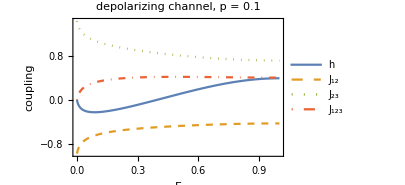

```mathematica
plotDepolarizing = Plot[{
h1+h2+h3,
J12,
J23,
J123
} /. mapping /. α->ArcSin[Sqrt[p]] /. p->0.1 //Evaluate, {Γ,0,1},Frame->True,
FrameStyle->Directive[Black,FontSize->14],PlotStyle -> {{}, {Dashed}, {Dotted}, {DotDashed}}, PlotLegends->{"h", "J_12", "J_23", "J_123"},
ImageSize->300, FrameLabel->{"Γ", "coupling"}, PlotLabel -> Style["depolarizing channel,  p = 0.1", {Black,FontSize->14}]]
```

### With Dissipation — “Spontaneous Emission Channel”

```mathematica
(* same spiel, different Kraus operators *)
wd2 = Table[Sum[τTensor⟦σ,a1,b1,a2,b2⟧ * 
                                    KrausSpont⟦m1,a1,aa1⟧ * KrausSpontConj⟦m1,b1,bb1⟧ *
							       KrausSpont⟦m2,a2,aa2⟧ * KrausSpontConj⟦m2,b2,bb2⟧ *
							       Measurement⟦aa1,bb1,aa2,bb2,A1,B1,A2,B2⟧ * σTensor⟦τ,A1,B1,A2,B2⟧,
	{a1,1,q}, {b1,1,q}, {a2,1,q}, {b2,1,q}, {A1,1,q}, {B1,1,q}, {A2,1,q}, {B2,1,q},
	{aa1,1,q}, {bb1,1,q}, {aa2,1,q}, {bb2,1,q},
	{m1,1,Length[KrausSpont]}, {m2,1,Length[KrausSpont]}],
	{σ,1,2}, {τ,1,2}] //Simplify
```

(2 ((2-2 Γ+Γ^2) Cos[α]^4+(1-Γ+Γ^2) Sin[α]^4) | 2 (Cos[α]^4+(1-Γ+Γ^2) Sin[α]^4)
1/2 (1+Γ^2) (3+Cos[4 α]) | 4 Cos[α]^4+2 (1+Γ^2) Sin[α]^4)

```mathematica
(* for small Γ, this expands to... *)
wd2smallΓ = Assuming[{Γ>0}, Normal[Series[wd2, {Γ,0,1}]]]
```

(2 (2 Cos[α]^4+Sin[α]^4)-2 Γ (2 Cos[α]^4+Sin[α]^4) | -2 Γ Sin[α]^4+2 (Cos[α]^4+Sin[α]^4)
1/2 (3+Cos[4 α]) | 4 Cos[α]^4+2 Sin[α]^4)

```mathematica
(* in terms of p, we have... *)
wd2smallΓ /. α -> ArcSin[Sqrt[p]] //Expand // TrigToExp //Simplify
```

(-2 (2-4 p+3 p^2) (-1+Γ) | 2-4 p-2 p^2 (-2+Γ)
2-4 p+4 p^2 | 4-8 p+6 p^2)

#### Boltzmann weights and classical model parameters (spontaneous emission)

```mathematica
boltzmannWeights = Table[Sum[Weingarten⟦σ3,τ⟧ * wd2⟦σ1,τ⟧ * wd2⟦σ2,τ⟧, {τ,1,2}], {σ1,1,2}, {σ2,1,2}, {σ3,1,2}];
mappingSpont = Thread[ClassicalMappingArgs -> ClassicalMapping.Flatten[Log[boltzmannWeights]]];
```

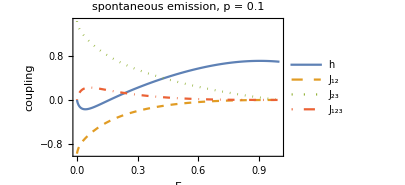

```mathematica
plotSpont = Plot[{
h1 + h2 + h3,
J12,
J23,
J123
}  /. mappingSpont /. α->ArcSin[Sqrt[p]] /. p->0.1 //Evaluate, {Γ,0,1},Frame->True,
FrameStyle->Directive[Black,FontSize->14],PlotStyle -> {{}, {Dashed}, {Dotted}, {DotDashed}}, PlotLegends->{"h", "J_12", "J_23", "J_123"},
ImageSize->300, FrameLabel->{"Γ", "coupling"}, PlotLabel -> Style["spontaneous emission,  p = 0.1", {Black,FontSize->14}]]
```

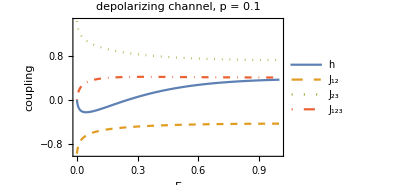
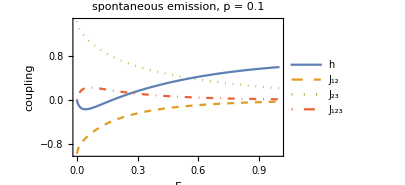
-Graphics- | -Graphics-

```mathematica
Grid[{{plotDepolarizing, plotSpont}}]
```